```mathematica
u090494e　荒井直幸　2014年12月16日
```

```mathematica
課題１
```

```mathematica
１）
```

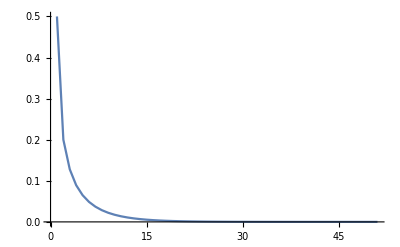

```mathematica
i=0;
table1={};
shoki=0.5;
AppendTo[table1,shoki];
While[i<50,
xx=0.8 shoki (1-shoki);
AppendTo[table1,xx];
shoki=xx;
i++]
graph1=ListPlot[table1,Joined->True,PlotRange->All]
```

```mathematica
２）
```

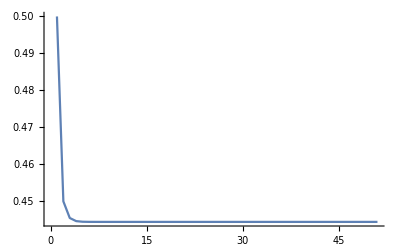

```mathematica
i=0;
table1={};
shoki=0.5;
AppendTo[table1,shoki];
While[i<50,
xx=1.8 shoki (1-shoki);
AppendTo[table1,xx];
shoki=xx;
i++]
graph2=ListPlot[table1,Joined->True,PlotRange->All]
```

```mathematica
３）
```

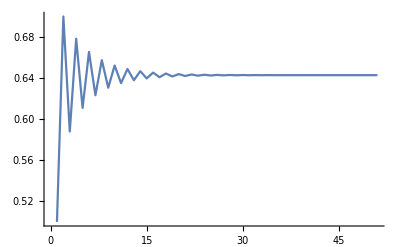

```mathematica
i=0;
table1={};
shoki=0.5;
AppendTo[table1,shoki];
While[i<50,
xx=2.8 shoki (1-shoki);
AppendTo[table1,xx];
shoki=xx;
i++]
graph3=ListPlot[table1,Joined->True,PlotRange->All]
```

```mathematica
４）
```

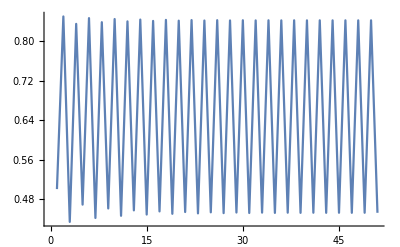

```mathematica
i=0;
table1={};
shoki=0.5;
AppendTo[table1,shoki];
While[i<50,
xx=3.4 shoki (1-shoki);
AppendTo[table1,xx];
shoki=xx;
i++]
graph4=ListPlot[table1,Joined->True,PlotRange->All]
```

```mathematica
５）
```

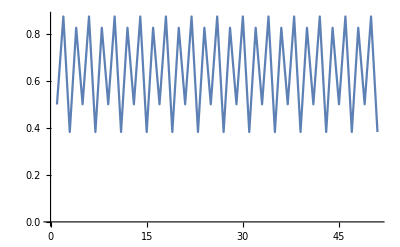

```mathematica
i=0;
table1={};
shoki=0.5;
AppendTo[table1,shoki];
While[i<50,
xx=3.5 shoki (1-shoki);
AppendTo[table1,xx];
shoki=xx;
i++]
graph5=ListPlot[table1,Joined->True,PlotRange->All]
```

```mathematica
６）
```

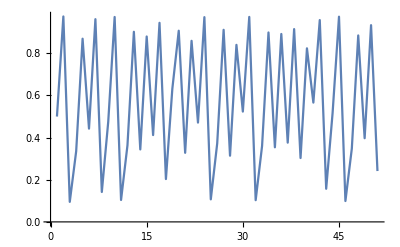

```mathematica
i=0;
table1={};
shoki=0.5;
AppendTo[table1,shoki];
While[i<50,
xx=3.9 shoki (1-shoki);
AppendTo[table1,xx];
shoki=xx;
i++]
graph6=ListPlot[table1,Joined->True,PlotRange->All]
```

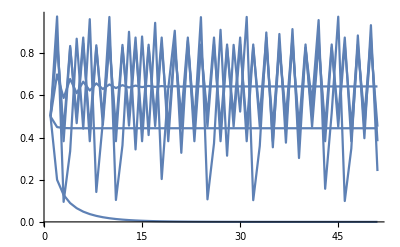

```mathematica
Show[graph1,graph2,graph3,graph4,graph5,graph6,PlotRange->All]
```

```mathematica
課題２
```

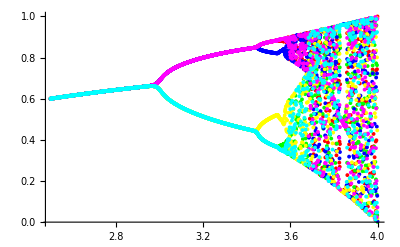

```mathematica
tablez={};
i=0;
hajime=2.5;
While[i<1500,
func1[x_]:=(2.5+i/1000) x (1-x);
kotae=FixedPoint[func1,0.5,101];
AppendTo[tablez,{2.5+i/1000,kotae}]
i++]
gra1=ListPlot[tablez,PlotRange->{0,1},PlotStyle->RGBColor[1,0,0]];
tablez1={};
i=0;
hajime=2.5;
While[i<1500,
func1[x_]:=(2.5+i/1000) x (1-x);
kotae1=FixedPoint[func1,0.5,102];
AppendTo[tablez1,{2.5+i/1000,kotae1}]
i++]
gra2=ListPlot[tablez1,PlotRange->{0,1},PlotStyle->RGBColor[0,1,0]];
tablez2={};
i=0;
hajime=2.5;
While[i<1500,
func1[x_]:=(2.5+i/1000) x (1-x);
kotae2=FixedPoint[func1,0.5,103];
AppendTo[tablez2,{2.5+i/1000,kotae2}]
i++]
gra3=ListPlot[tablez2,PlotRange->{0,1},PlotStyle->RGBColor[0,0,1]];
tablez3={};
i=0;
hajime=2.5;
While[i<1500,
func1[x_]:=(2.5+i/1000) x (1-x);
kotae3=FixedPoint[func1,0.5,104];
AppendTo[tablez3,{2.5+i/1000,kotae3}]
i++]
gra4=ListPlot[tablez3,PlotRange->{0,1},PlotStyle->RGBColor[1,1,0]];
tablez4={};
i=0;
hajime=2.5;
While[i<1500,
func1[x_]:=(2.5+i/1000) x (1-x);
kotae4=FixedPoint[func1,0.5,105];
AppendTo[tablez4,{2.5+i/1000,kotae4}]
i++]
gra5=ListPlot[tablez4,PlotRange->{0,1},PlotStyle->RGBColor[1,0,1]];
tablez5={};
i=0;
hajime=2.5;
While[i<1500,
func1[x_]:=(2.5+i/1000) x (1-x);
kotae5=FixedPoint[func1,0.5,106];
AppendTo[tablez5,{2.5+i/1000,kotae5}]
i++]
gra6=ListPlot[tablez5,PlotRange->{0,1},PlotStyle->RGBColor[0,1,1]];
Show[gra1,gra2,gra3,gra4,gra5,gra6,PlotRange->All]
```